```mathematica
Vred[n_,ϵ_,x_]:=-1/4 n (2 +ϵ+√(1+ϵ)2 Cos[2 2π x])
Vblue[n_,ϵ_,x_]:=1/4 n (2 +ϵ-√(1+ϵ)2 Cos[2 2π x])
```

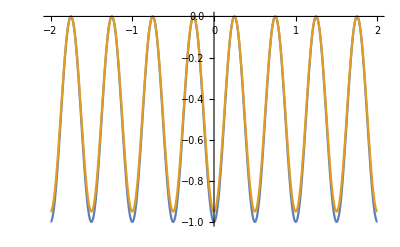

```mathematica
Plot[{Vred[1,0,x],Vred[1,-0.1,x]},{x,-2,2}]
```

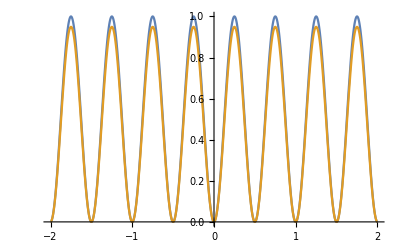

```mathematica
Plot[{Vblue[1,0,x],Vblue[1,-0.1,x]},{x,-2,2}]
```

```mathematica
Egr[ϵ_,n_]:=(2+ϵ+2 √(1+ϵ))/4 n+ 2 √n(1+ϵ)^(1/4)
DEgr[ϵ_,n_]:=Egr[ϵ,n]-Egr[0,n]
Egb[ϵ_,n_]:=(2+ϵ-2 √(1+ϵ))/4 n+ 2 √n(1+ϵ)^(1/4)
DEgb[ϵ_,n_]:=Egb[ϵ,n]-Egb[0,n]
```

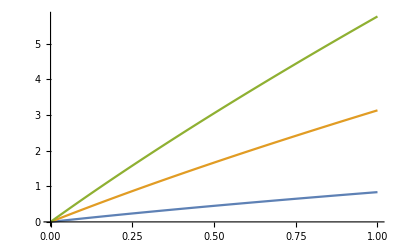

```mathematica
Plot[{DEgr[x,1],DEgr[x,5],DEgr[x,10]},{x,0,1}]
```

```mathematica
Series[Log[x],{x,0}]
```

Series::sspec: Series specification {x,0} is not a list with three elements.

```mathematica
Series[x Log[1+x],{x,0,5}]
```

x^2-x^3/2+x^4/3-x^5/4+O[x]^6

```mathematica
h=6.626 10^-34;
hbar=1.0545 10^-34
kb=1.38 10^-23;
mrb=87 1.66 10^-27;
mrb2=87 1.42 10^-25/85;
T=1 10^-9;
λ=h/(√(2 π mrb kb T))
λ=√((2 π hbar^2)/(mrb kb T))
```

1.0545×10^-34

5.92118×10^-6

5.92084×10^-6

```mathematica
8.7/6
```

1.45

```mathematica
N[√(4 110^2+870^2)]
```

897.385

```mathematica
N[410*5/4]
```

512.5

```mathematica
N[Log[3]]
```

1.09861

```mathematica
N[(√6)]
N[(√6+1)/2]
N[(√2)]
```

2.44949

1.72474

1.41421

```mathematica
N[(3+2)/3]
```

1.66667

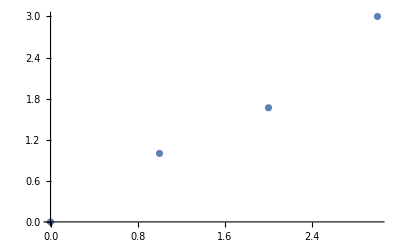

```mathematica
ListPlot[{{0,0},{1,1},{2,5/3},{3,3}}]
```